# Usmrtitve v ZDA

## Analiza usmrtitev v ZDA glede na različne dejavnike .

## Pridobivanje podatkov

Podatke sem pridobila iz podatkovne baze Wolfram data repository.

```mathematica
podatki = ResourceData["Executions in the United States"]
```

Dataset[<>]

## Analiza podatkov o usmrtitvah glede na spol, starost ter raso

Analizirala ter narisala bom nekaj grafov števila usmrtitev glede na spol, starost ter raso. Podatki so obdelani ter predstavljeni tudi z grafi.

V spremenljivki spolM je shranjeno število moških, ki so jih usmrtili (to je število 1465), v spremenljivki spolZ pa stevilo zensk (to je število 16)

```mathematica
spolM = Length[Select[podatki,#["Sex"]=="m" &]]
```

1465

```mathematica
spolZ= Length[Select[podatki,#["Sex"]=="f" &]]
```

16

V seznamu z imenom seznamStarosti so zbrani podatki o starosti ljudi, ki so jih usmrtili. Podatki so prikazani tudi z histogramom.

```mathematica
seznamStarosti= podatki[All,"Age"];
```

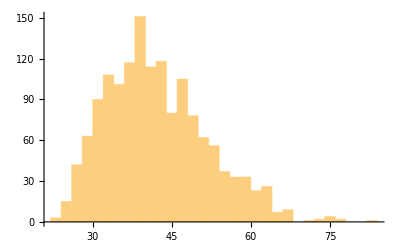

```mathematica
Histogram[seznamStarosti]
```

V seznamu z imenom seznamZenske so zbrani podatki o starosti žensk in spodaj prikazani z histogramom.

```mathematica
seznamZenske =Select[podatki,#["Sex"]=="f" &][All,"Age"];
```

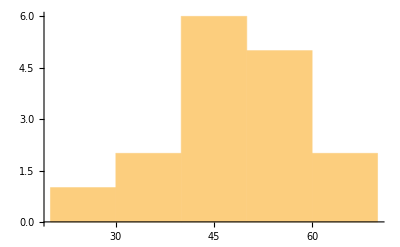

```mathematica
Histogram[seznamZenske]
```

V seznamu z imenom seznamMoski so zbrani podatki o starosti moških in spodaj prikazani z histogramom.

```mathematica
seznamMoski=Select[podatki,#["Sex"]=="m" &][All,"Age"];
```

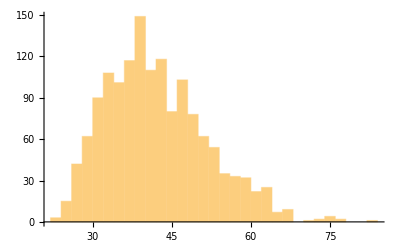

```mathematica
Histogram[seznamMoski]
```

V funkciji SteviloRasa kot argument podamo raso in izpišemo število ljudi glede na raso.
To funkcijo spodaj nato pokličem in ji kot argument podam tri rase: White, Black in pa Latino.
Podatke o vseh treh rasah shranim v seznam z imenom seznamPoRasah.

```mathematica
SteviloRasa[rasa_]:=Length[Select[podatki,#["Race"]==rasa&]]
```

```mathematica
seznamPoRasah=SteviloRasa/@{"White","Black","Latino"}
```

{824,508,124}

Zgoraj zbrane podatke o rasah predstavim v obliki tortnega diagrama, ki ima tudi legendo, ki prikazuje katero barvo predstavlja katera rasa.

```mathematica
PieChart3D[seznamPoRasah,ChartLegends->{"White","Black","Latino"}]
```

-Graphics3D-

## Analiza glede na čas

```mathematica
seznamDatumov=podatki[All,"Date"];
```

```mathematica
seznamLetnic=DateObject[#,"Year"]&/@seznamDatumov
```

```mathematica
Stevilo[letnica_]:={letnica,Count[seznamLetnic,letnica]}
```

```mathematica
SteviloPoLetnicah=Stevilo/@(seznamLetnic//DeleteDuplicates)
```

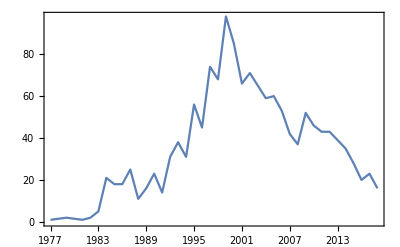

```mathematica
DateListPlot[SteviloPoLetnicah]
```

## Analiza podatkov po državah

Analizirala bom, če obstaja kakšna povezava med številom ljudi, ki jih usmrtijo, ter državo oz. okolico iz katere prihajajo. Na grafu bom prikazala število usmrtitev po državah.

## Analiza še glede na ostale dejavnike

Raziskala bom podatke - o načinih usmrtitev, o ozadju tistih, ki so jih oz . jih bojo usmrtili (ali so bili že kot mlajši problematični in v zaporu za mladostnike, ali so bili kdaj v življenju prostovoljci), o razmerju usmrčenih državljanov ZDA ter tujcih in o številu žrtev .